# Finite N Sachdev-Ye-Kitaev model

## Direct diagonalization of the SYK Hamiltonian to analyze its spectral properties. We practice working with large matrices, memoization, function compilation, and various optimization techniques.

## Preliminaries

We will want to save data, so better have it in the Notebook’s directory

```mathematica
SetDirectory@NotebookDirectory[];
```

Mathematica 12’s compilation to C is sometimes a bit broken in Windows

```mathematica
Needs["CCompilerDriver`"];
```

```mathematica
$CCompiler={"Name"->"Generic C Compiler","Compiler"->CCompilerDriver`GenericCCompiler`GenericCCompiler,"CompilerInstallation"->"C:\\TDM-GCC-64\\bin","CompilerName"->"gcc.exe"};
```

## KroneckerProduct implementation of Dirac gamma matrices

There is a different implementation at the end of this notebook. For the purposes of this problem, this more naive implementation is actually better.

### Recursive definition of Gamma matrices

```mathematica
ClearAll@𝟙;
𝟙[n_Integer]:=𝟙[n]=IdentityMatrix[2^Floor[n/2],SparseArray];
```

```mathematica
ClearAll@Γ;
Γ[2][1]=SparseArray@PauliMatrix@1;
Γ[2][2]=SparseArray@PauliMatrix@2;
Γ[n_Integer?EvenQ][a_Integer]/;a≤n-2:=Γ[n][a]=KroneckerProduct[Γ[n-2][a],PauliMatrix@3];
Γ[n_Integer?EvenQ][a_Integer]/;a==n-1:=Γ[n][a]=-KroneckerProduct[𝟙[n-2],PauliMatrix@1];
Γ[n_Integer?EvenQ][a_Integer]/;a==n:=Γ[n][a]=-KroneckerProduct[𝟙[n-2],PauliMatrix@2];
Γ[n_Integer?OddQ][a_Integer]/;a<n:=Γ[n][a]=Γ[n-1][a];
Γ[n_Integer?OddQ][a_Integer]/;a==n:=Γ[n][a]=ⅈ^((n-1)/2) Dot@@Table[Γ[n-1][i],{i,n-1}];
```

#### Check commutation relations

```mathematica
And@@Flatten@Table[Γ[n][i].Γ[n][j]+Γ[n][j].Γ[n][i]==2KroneckerDelta[i,j]𝟙[n],{n,2,26},{i,n},{j,n}]
```

True

### Memoizing Gamma matrix products can save time

```mathematica
Γ[n_Integer][a_Integer,b_Integer]/;1≤a<b≤n:=Γ[n][a,b]=Γ[n][a].Γ[n][b];
Γ[n_Integer][a_Integer,b_Integer,c_Integer,d_Integer]/;1≤a<b<c<d≤n:=Γ[n][a,b,c,d]=Γ[n][a,b].Γ[n][c,d];
```

## Definition of the SYK Hamiltonian

### The Hamiltonian and random couplings

```mathematica
Coupling[n_Integer]:=RandomVariate@NormalDistribution[0,√(6/n^3)];
```

```mathematica
ClearAll@H;
H[n_Integer]:=1/4 Sum[Coupling@n Γ[n][i,j,k,l],{l,n},{k,l-1},{j,k-1},{i,j-1}]
```

### Direct diagonalization (including matrix deflation)

```mathematica
ClearAll@P;
P[n_Integer]:=P[n]=Sort/@ConnectedComponents@AdjacencyGraph@Unitize@H[n];
```

```mathematica
ClearAll@Spectrum;
Spectrum[n_Integer]:=Sort@Flatten[Eigenvalues/@(H[n]⟦#,#⟧&/@P[n])]
```

### Timings

#### Hamiltonian construction

These timings were run on different days with various other tasks in the background. Though not the best of settings, they still show construction time for the SYK Hamiltonian is ~10^-5 2^n s

```mathematica
AbsoluteTiming@H[20]
```

{1.06081,SparseArray[<262144>, {1024, 1024}]}

```mathematica
AbsoluteTiming@H[22]
```

{4.08424,SparseArray[<790528>, {2048, 2048}]}

```mathematica
AbsoluteTiming@H[24]
```

{14.1127,SparseArray[<2301952>, {4096, 4096}]}

```mathematica
AbsoluteTiming@H[26]
```

{65.1826,SparseArray[<6504448>, {8192, 8192}]}

```mathematica
AbsoluteTiming@H[28]
```

{141.937,SparseArray[<17907712>, {16384, 16384}]}

```mathematica
AbsoluteTiming@H[30]
```

{304.624,SparseArray[<48201728>, {32768, 32768}]}

```mathematica
ConstructionTimingData={{20,1.0608121},{22,4.0842424},{24,14.1126916},{26,65.1826217},{28,141.9368386},{30,304.6240726}};
```

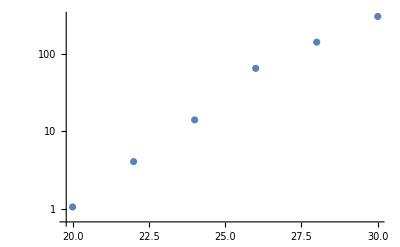

```mathematica
ListLogPlot@ConstructionTimingData
```

```mathematica
ConstructionTimingFit=LinearModelFit[{First@#,Log@Last@#}&/@ConstructionTimingData,n,n]
```

FittedModel[-11.2946+0.578215 n]

```mathematica
Exp@ConstructionTimingFit["BestFitParameters"]
```

{0.0000124403,1.78285}

#### Hamiltonian diagonalization

These timings should be run twice, since the first time there is an overhead in the pre-computation of the matrix deflation splitting.

```mathematica
Dynamic@n
```

```mathematica
DiagonalizationTimingData=Table[{n,First@AbsoluteTiming@Spectrum@n},{n,20,26,2}]
```

Eigenvalues::arh: Because finding 4096 out of the 4096 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

{{20,2.40166},{22,7.86442},{24,30.1553},{26,126.004}}

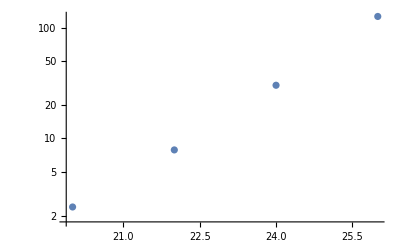

```mathematica
ListLogPlot@DiagonalizationTimingData
```

```mathematica
DiagonalizationTimingFit=LinearModelFit[{First@#,Log@Last@#}&/@DiagonalizationTimingData⟦-3;;⟧,n,n]
```

FittedModel[-13.2088+0.69349 n]

```mathematica
Exp@DiagonalizationTimingFit["BestFitParameters"]
```

{1.83445×10^-6,2.00069}

```mathematica
SaveData[30][3]//AbsoluteTiming
```

Eigenvalues::arh: Because finding 16384 out of the 16384 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

{2859.05,Null}

## Data generation and loading

```mathematica
SaveData[n_Integer][k_Integer]:=
Block[{filename=FileNameJoin@{"SYKdata","n"<>ToString@n<>".evs"},stream},
stream=OpenAppend[filename,BinaryFormat->True];
Do[BinaryWrite[stream,Spectrum[n],"Real64"],{r,k}];
Close@stream;
]
```

```mathematica
CountData[n_Integer]:=
Block[{filename="SYKdata\\n"<>ToString@n<>".evs",stream,res},
stream=OpenRead[filename,BinaryFormat->True];
res=2^(-Floor[n/2])Length@BinaryReadList[stream,"Real64"];
Close@stream;
res
]
```

```mathematica
LoadData[n_Integer]:=
Block[{filename="SYKdata\\n"<>ToString@n<>".evs",stream,data},
stream=OpenRead[filename,BinaryFormat->True];
data=Partition[BinaryReadList[stream,"Real64"],2^Floor[n/2]];
Close@stream;
SpectrumData[n]=data
]
```

#### Generate some data for later use

```mathematica
Dynamic@{n,r}
```

```mathematica
Do[SaveData[n]@Ceiling[2^(-Floor[n/2])2^18],{n,10,30}]
```

Eigenvalues::arh: Because finding 4096 out of the 4096 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

```mathematica
CountData/@Range[10,30]
```

{8192,8192,4096,4096,2048,2048,1024,1024,512,512,256,256,128,128,64,64,32,32,16,16,8}

#### Load pre-generated data

```mathematica
LoadData/@Range[10,30];
```

## Some results

### Density of states

We can plot an estimation for the density of states using SmoothHistogram and related functions.

```mathematica
ClearAll@RhoPlot;
RhoPlot[n_Integer][color_]:=
With[{ρ=PDF@SmoothKernelDistribution@Flatten@SpectrumData@n},
Plot[ρ[x],{x,-1.6,1.6},PlotStyle->color,PlotLegends->LineLegend[{color},{"N = "<>ToString@n}],AxesLabel->{"E","(ρ (E))/2^[N/2]"},ImageSize->1024,AxesStyle->Black,TicksStyle->Medium]
]
```

```mathematica
MyColor[n_]:=ColorData["Rainbow"][(n-10)/(30-10)]
```

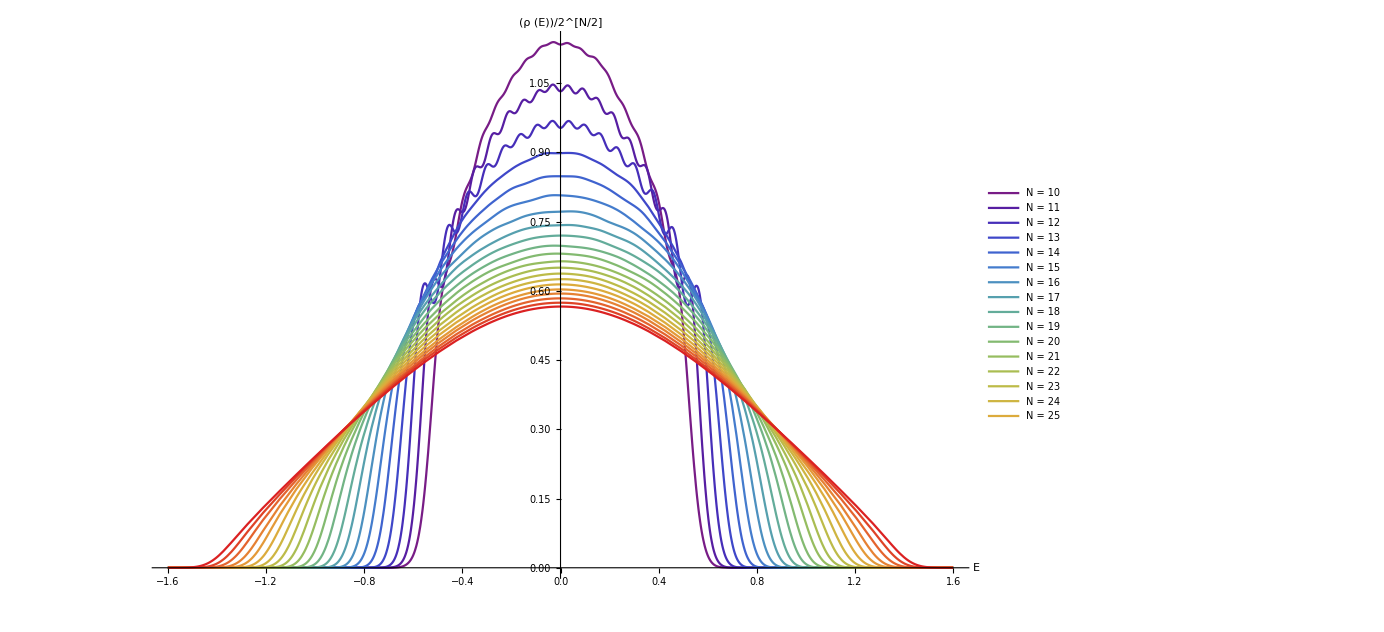

```mathematica
Show@Table[RhoPlot[n][MyColor@n],{n,10,30}]
```

```mathematica
Export["rho.pdf",%]
```

rho.pdf

### Entropy

We can estimate the large-N high-temperature entropy by extrapolating the density of states around the center of the spectrum.
Similarly, we can estimate the large-N low-temperature entropy by extrapolating the density of states around the groundstate.

```mathematica
SpectrumCentralBand[n_Integer][w_Real]:=N@MeanAround@Table[Count[evs,E_Real/;-w/2<E<w/2],{evs,SpectrumData@n}];
SpectrumGSBand[n_Integer][w_Real]:=N@MeanAround@Table[Count[evs,E_Real/;E-Min@evs<w],{evs,SpectrumData@n}];
```

```mathematica
CentralBand=Table[{n,Log@SpectrumCentralBand[n][.3]},{n,10,30,2}]
```

{{10,2.38440.0011},{12,2.88120.0016},{14,3.47900.0008},{16,4.07840.0009},{18,4.70210.0006},{20,5.33870.0007},{22,5.98660.0006},{24,6.64020.0007},{26,7.29740.0007},{28,7.95840.0008},{30,8.62070.0010}}

```mathematica
CentralBandFit=LinearModelFit[CentralBand⟦-3;;⟧/.Around[x_,_]:>x,n,n]
```

FittedModel[-1.30386+0.330811 n]

```mathematica
GSBand=Table[{n,Log@SpectrumGSBand[n][.3]},{n,10,30,2}]
```

{{10,2.16520.0017},{12,2.72970.0019},{14,3.14290.0018},{16,3.60010.0025},{18,4.05860.0027},{20,4.57420.0033},{22,5.01900.0034},{24,5.4990.005},{26,5.9840.006},{28,6.4890.006},{30,6.9510.008}}

```mathematica
GSBandFit=LinearModelFit[GSBand⟦-3;;⟧/.Around[x_,_]:>x,n,n]
```

FittedModel[-0.290225+0.241602 n]

The plot below has its error bars hidden by the point markers.

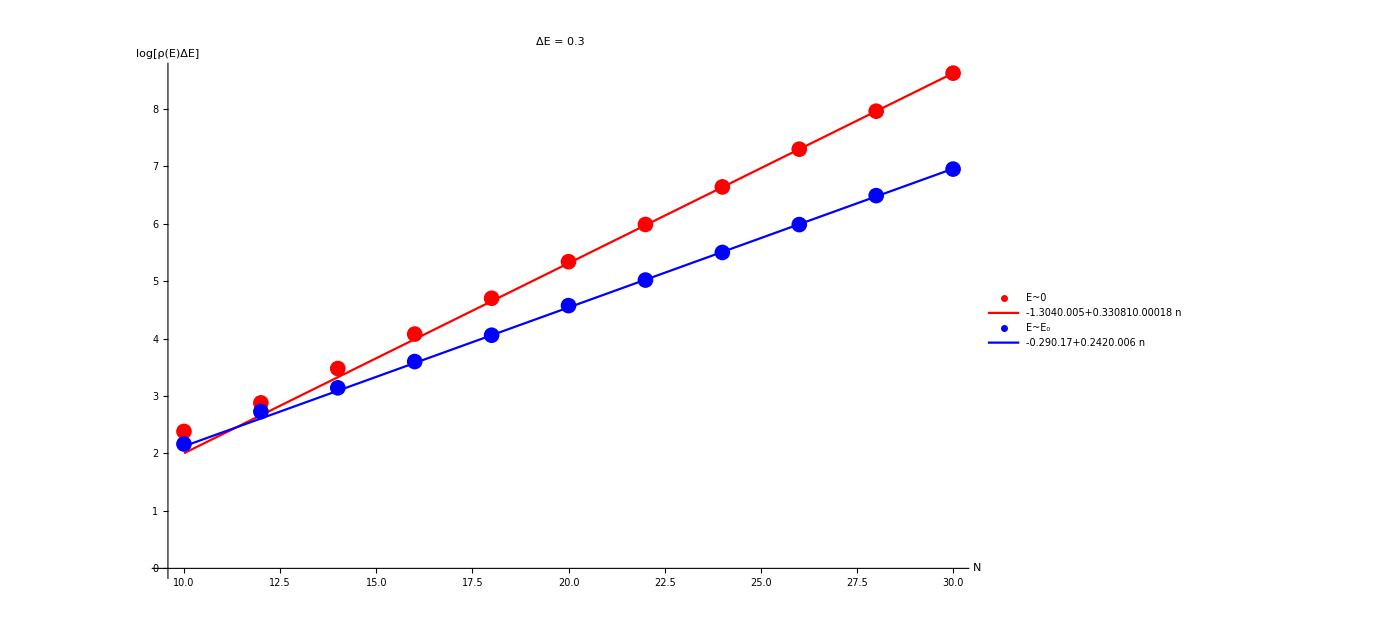

```mathematica
Show[{
ListPlot[CentralBand,PlotStyle->Red,PlotLegends->PointLegend[{Red},{"E~0"}]],
Plot[CentralBandFit[n],{n,10,30},PlotStyle->Red,PlotLegends->LineLegend[{Red},{{1,n}.Around@@@Transpose@{CentralBandFit["BestFitParameters"],CentralBandFit["ParameterErrors"]}}]],
ListPlot[GSBand,PlotStyle->Blue,PlotLegends->LineLegend[{Blue},{"E~E_0"}]],
Plot[GSBandFit[n],{n,10,30},PlotStyle->Blue,PlotLegends->LineLegend[{Blue},{{1,n}.Around@@@Transpose@{GSBandFit["BestFitParameters"],GSBandFit["ParameterErrors"]}}]]
},ImageSize->1024,AxesLabel->{"N","log[ρ(E)ΔE]"},AxesStyle->Black,TicksStyle->Medium,PlotLabel->"ΔE = 0.3"]
```

```mathematica
Export["entropy.pdf",%]
```

entropy.pdf

### Spectral form factor

To speed up the evaluation of spectral form factors, we pre-compile the partition functions for each realization of the Hamiltonians we have already diagonalized.

```mathematica
ClearAll@CompiledZs;
CompiledZs[n_Integer]:=CompiledZs[n]=Table[Compile[{{β,_Complex}},Evaluate@Total[ⅇ^(-β evs)]],{evs,SpectrumData@n}];
```

```mathematica
ClearAll@SFF;
SFF[n_Integer][β_Real,t_Real]:=Mean@Table[((Abs@Z[β+ⅈ t])/Z[β])^2,{Z,CompiledZs@n}]
```

```mathematica
Dynamic@{n,t}
```

```mathematica
ClearAll@SFFPlot;
SFFPlot[n_Integer][β_Real,mint_,maxt_,numt_Integer][color_]:=SFFPlot[n][β,mint,maxt,numt][color]=
ListLogLogPlot[Table[{t,SFF[n][β,t]},{t,10.^Range[mint,maxt,(maxt-mint)/(numt-1)]}],Joined->True,PlotRange->All,PlotStyle->color,ImageSize->1024,AxesLabel->{"t","f_β(t)"},AxesStyle->Black,TicksStyle->Medium,PlotLegends->LineLegend[{color},{"N = "<>ToString@n}]]
```

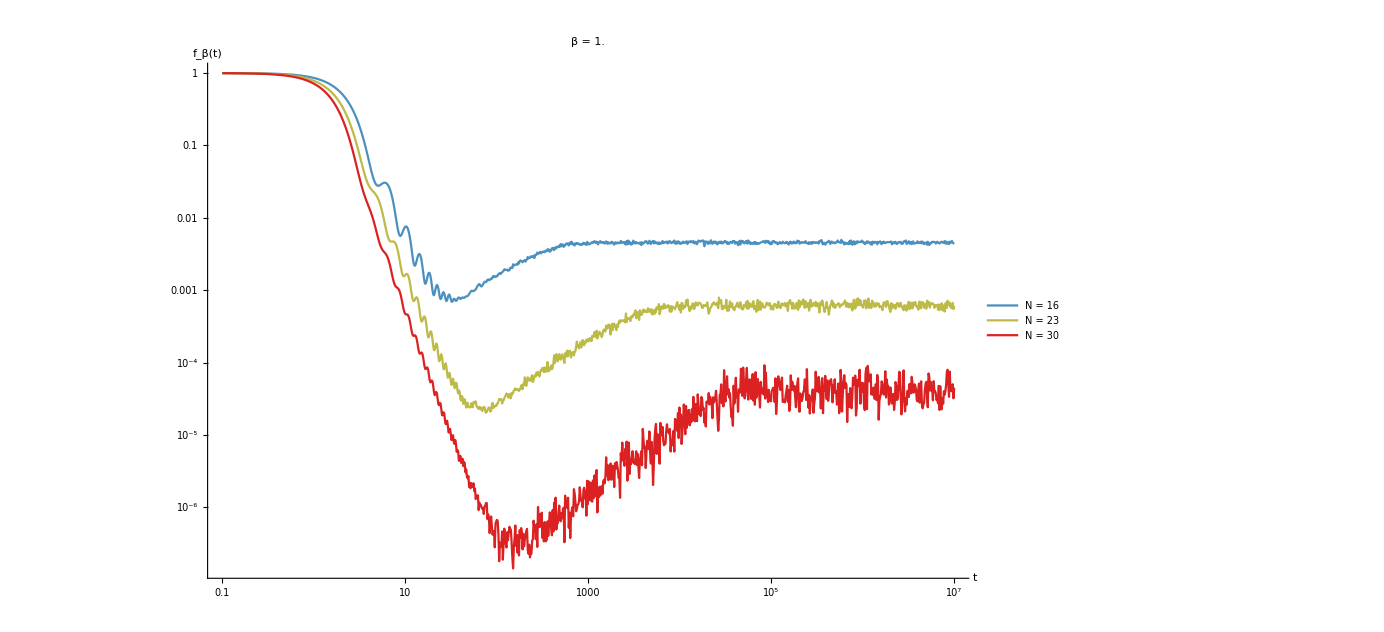

```mathematica
With[{β=1.},
Show[
Table[SFFPlot[n][β,-1,7,1000][MyColor@n],{n,{16,23,30}}]
,PlotLabel->"β = "<>ToString@β,PlotRange->All,AxesOrigin->{-2.3,-16.125}
]
]
```

```mathematica
Export["SFF.pdf",%]
```

SFF.pdf

## Symbolic implementation of Dirac gamma functions

### Recursive definition of symbolic Gamma matrices

```mathematica
ClearAll@id;
id[n_Integer]:=id[n]=CircleTimes@@Table[s𝟙,{Floor[n/2]}];
```

```mathematica
ClearAll@CircleTimes;
SetAttributes[CircleTimes,Flat];
CircleTimes[x___,a_ y_,z___]/;FreeQ[a,s𝟙]&&FreeQ[a,σ]:=a CircleTimes[x,y,z];
```

```mathematica
ClearAll@CenterDot;
CenterDot[x___,u_+v_,y___]:=CenterDot[x,u,y]+CenterDot[x,v,y];
CenterDot[x___,a_ y_,z___]/;FreeQ[a,s𝟙]&&FreeQ[a,σ]:=a CenterDot[x,y,z];
CenterDot[x___,CircleTimes@u__,CircleTimes@v__,y___]:=CenterDot[x,Inner[CenterDot,{u},{v},CircleTimes],y];
CenterDot[x_]:=x;
CenterDot[x___,s𝟙,y___]:=CenterDot[x,y];
CenterDot[x___,σ[a_],σ[b_],y___]:=KroneckerDelta[a,b]CenterDot[x,s𝟙,y]+ⅈ Sum[CenterDot[x,σ[c],y]Signature@{a,b,c},{c,3}];
```

```mathematica
ClearAll@sΓ;
sΓ[2][1]=σ[1];
sΓ[2][2]=σ[2];
sΓ[n_Integer?EvenQ][a_Integer]/;1≤a≤n-2:=sΓ[n][a]=CircleTimes[sΓ[n-2][a],σ[3]];
sΓ[n_Integer?EvenQ][a_Integer]/;a==n-1:=sΓ[n][a]=-CircleTimes[id[n-2],σ[1]];
sΓ[n_Integer?EvenQ][a_Integer]/;a==n:=sΓ[n][a]=-CircleTimes[id[n-2],σ[2]];
sΓ[n_Integer?OddQ][a_Integer]/;a<n:=sΓ[n][a]=sΓ[n-1][a];
sΓ[n_Integer?OddQ][a_Integer]/;a==n:=sΓ[n][a]=ⅈ^((n-1)/2) CenterDot@@Table[sΓ[n-1][i],{i,n-1}];
```

```mathematica
ExpRep={s𝟙->IdentityMatrix[2,SparseArray],σ->(SparseArray@PauliMatrix@#&)};
```

#### Check that this definition coincides with the previous one upon replacement

```mathematica
And@@Flatten@Table[sΓ[n][i]==Γ[n][i]/.ExpRep/.CircleTimes->KroneckerProduct,{n,2,30},{i,n}]
```

True

#### Check the anti-commutation relations symbolically

This should be much faster than before, because no large matrices ever intervene.

```mathematica
And@@Flatten@Table[sΓ[n][i]·sΓ[n][j]+sΓ[n][j]·sΓ[n][i]==2id[n]KroneckerDelta[i,j],{n,4,30},{i,n},{j,n}]
```

True

### Construct the SYK Hamiltonian

We construct the Hamiltonian operating with Pauli matrices symbolically and only perform the KroneckerProduct’s in the end.
We memoize partial KroneckerProduct’s to save some time.

```mathematica
ClearAll@EvalCircleTimes;
EvalCircleTimes[x_]:=x/.ExpRep;
EvalCircleTimes[x__,y_]:=EvalCircleTimes[x,y]=KroneckerProduct[EvalCircleTimes[x],y/.ExpRep]
```

```mathematica
ClearAll@sH;
sH[n_Integer]:=1/4 Sum[Coupling@n sΓ[n][i]·sΓ[n][j]·sΓ[n][k]·sΓ[n][l]/.CircleTimes->EvalCircleTimes,{l,n},{k,l-1},{j,k-1},{i,j-1}]
```

#### Timings

These timings show symbolic evaluation is not necessarily better than the naive approach in this case.

```mathematica
sH[20]//AbsoluteTiming
```

{1.6622,SparseArray[<262144>, {1024, 1024}]}

```mathematica
sH[22]//AbsoluteTiming
```

{3.89529,SparseArray[<790528>, {2048, 2048}]}

```mathematica
sH[24]//AbsoluteTiming
```

{7.98945,SparseArray[<2301952>, {4096, 4096}]}

```mathematica
sH[26]//AbsoluteTiming
```

{65.6339,SparseArray[<6504448>, {8192, 8192}]}

```mathematica
sH[28]//AbsoluteTiming
```

{259.154,SparseArray[<17907712>, {16384, 16384}]}

```mathematica
sConstructionTimingData={{20,1.6622031},{22,3.8952901},{24,7.9894525},{26,65.6339138},{28,259.1538765}};
```

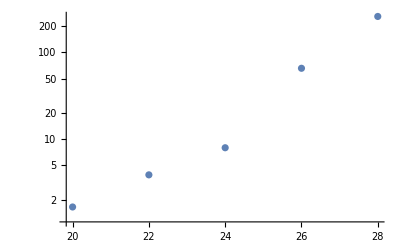

```mathematica
ListLogPlot@sConstructionTimingData
```

```mathematica
sConstructionTimingFit=LinearModelFit[{First@#,Log@Last@#}&/@sConstructionTimingData,n,n]
```

FittedModel[-12.7699+0.646144 n]

```mathematica
Exp@sConstructionTimingFit["BestFitParameters"]
```

{2.845×10^-6,1.90817}